```mathematica
Needs["FourierSeries`"]
```

```mathematica
Dens[en_]:=NFourierTransform[(BesselJ[0,t/Sqrt[6]])^3/Sqrt[2Pi],t,en]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-4.81037×10^7}. NIntegrate obtained 0.0048501  + 1.38778×10^-17\ ⅈ and 0.000605522 for the integral and error estimates.

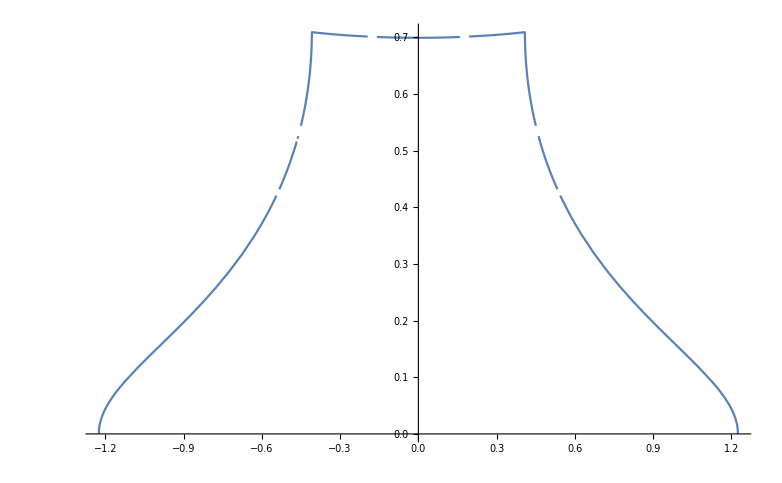

```mathematica
Plot[Dens[x],{x,-Sqrt[6]/2,Sqrt[6]/2}]
```

```mathematica
Denstab={N@#,N@Dens[#]}&/@Table[(Sqrt[6]/2)*i/1000,{i,-1000,1000}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-4.81037×10^7}. NIntegrate obtained 0.000241241  + 0.\ ⅈ and 0.00214756 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.81037×10^7}. NIntegrate obtained 0.0241122  + 0.\ ⅈ and 8.56765×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.81037×10^7}. NIntegrate obtained 0.0341255  + 5.63785×10^-17\ ⅈ and 1.43846×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{{-1.22474,0.0000962414+0. ⅈ},{-1.22352,0.00961938+0. ⅈ},{-1.2223,0.0136141+2.24918×10^-17 ⅈ},{-1.22107,0.0166863+0. ⅈ},{-1.21985,0.0192822+0. ⅈ},1991,{1.21985,0.0192822+0. ⅈ},{1.22107,0.0166863+0. ⅈ},{1.2223,0.0136141-2.24918×10^-17 ⅈ},{1.22352,0.00961938+0. ⅈ},{1.22474,0.0000962414+0. ⅈ}}
 |  |  |  |

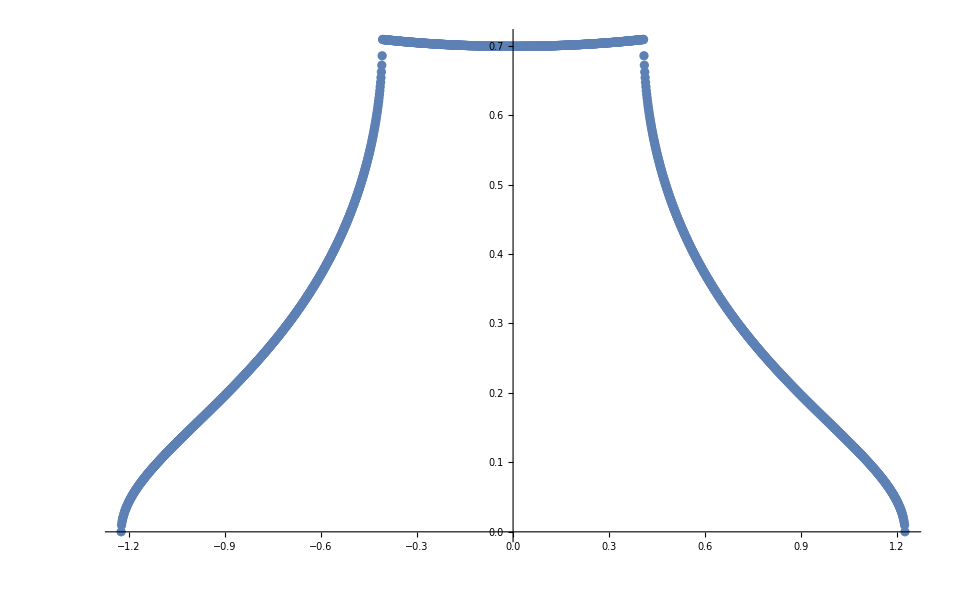

```mathematica
Show[{ListPlot[Denstab]}]
```

```mathematica
Export["dens3d.dat",Denstab]
```

dens3d.dat

```mathematica
betatab={13.0,14.0,15.6,17.4,19.6,22.4,26.1,32.4,39.4,52.8,65.0,80.0}
```

{13.,14.,15.6,17.4,19.6,22.4,26.1,32.4,39.4,52.8,65.,80.}

```mathematica
occup[beta_,en_]=Dens[en]/(Exp[beta*en]+1)
```

(4 EllipticK[1-en^2])/((1+ⅇ^(beta en)) π^2)

```mathematica
occup1[beta_]:=({N@#1,N@occup[beta,#1]}&/@Table[i/10000,{i,-10000,10000}])
```

```mathematica
Export["occup_beta"<>ToString[#]<>"0.dat",occup1[#]]&/@betatab
```

{occup_beta26.0.dat,occup_beta27.0.dat,occup_beta28.0.dat,occup_beta29.0.dat,occup_beta30.0.dat,occup_beta31.0.dat,occup_beta32.0.dat,occup_beta33.0.dat,occup_beta34.0.dat,occup_beta35.0.dat,occup_beta40.0.dat,occup_beta60.0.dat,occup_beta80.0.dat}

```mathematica
beta1tab:=Table[i,{i,26,1000}]
```

```mathematica
ekin1tab:={#,ekin[#]}&/@beta1tab
```

```mathematica
Export["Ekin1U0.dat",ekin1tab]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

Ekin1U0.dat

```mathematica
f[t_]=FullSimplify@FourierTransform[1/(1+Exp[x*2]),x,t]
```

-1/2 ⅈ √(π/2) Csch[(π t)/2]+√(π/2) DiracDelta[t]

```mathematica
ekin[b_]:=-(Sqrt[1.5]/b)NIntegrate[(BesselJ[0,x/Sqrt[6]])^2*BesselJ[1,x/Sqrt[6]]/Sinh[Pi*x/b],{x,-Infinity,+Infinity}]
```

```mathematica
%*(-1)*Sqrt[1.5]/20.0
```

-0.403484

```mathematica
FullSimplify@Integrate[(BesselJ[0,x])^2*BesselJ[1,x]/x,{x,-Infinity,+Infinity}]
```

MeijerG[{{1/2},{3/2,3/2}},{{0,1},{0}},1/4]/(√π)

```mathematica
-Sqrt[3/2]*%/Pi
```

-(√(3/2) MeijerG[{{1/2},{3/2,3/2}},{{0,1},{0}},1/4])/π^(3/2)

```mathematica
N@%
```

-0.409236

```mathematica
ekintab={#,ekin[#]}&/@Table[8.0+92.0*i/10000,{i,0,10000}]
```

{{8.,-0.375799},{8.0092,-0.375867},{8.0184,-0.375934},{8.0276,-0.376001},{8.0368,-0.376069},{8.046,-0.376136},{8.0552,-0.376202},{8.0644,-0.376269},{8.0736,-0.376335},9983,{99.9264,-0.409006},{99.9356,-0.409006},{99.9448,-0.409006},{99.954,-0.409006},{99.9632,-0.409006},{99.9724,-0.409006},{99.9816,-0.409006},{99.9908,-0.409006},{100.,-0.409006}}
 |  |  |  |

```mathematica
Export["EkinU0.dat",ekintab]
```

EkinU0.dat